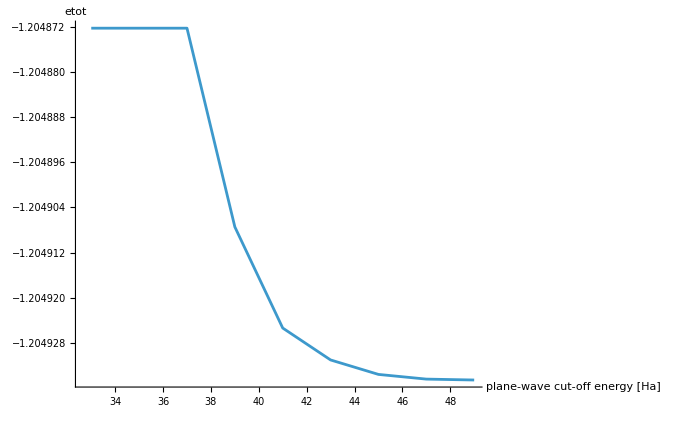

```mathematica
data={
{33,-1.20487228},
{35,-1.20487228},
{37,-1.20487228},
{39,-1.20490746},
{41,-1.20492536},
{43,-1.20493101},
{45,-1.20493357},
{47,-1.20493440},
{49,-1.20493456}
};
ListLinePlot[data,
PlotRange->{All,All},
AxesLabel->{"plane-wave cut-off energy [Ha]", "etot"}
]
```

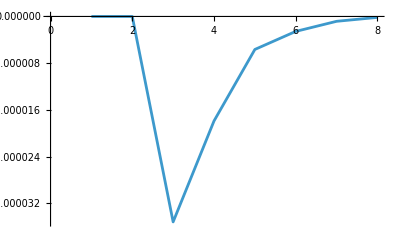

```mathematica
ListLinePlot@Differences@data[[All,2]]
```

## Retrying with tsmear 0.01 and ngkpt 4 4 4

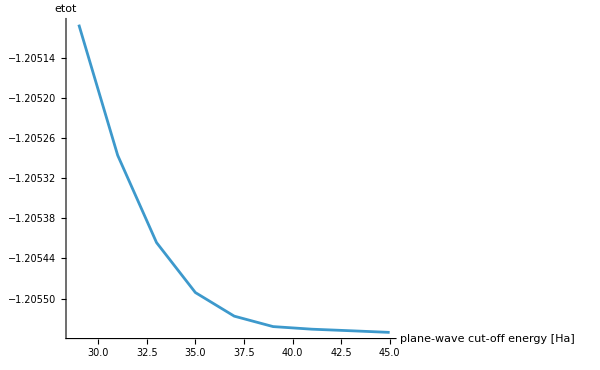

{-0.000195684,-0.000130738,-0.0000748815,-0.0000353508,-0.0000156378,-3.8979×10^-6,-2.3512×10^-6,-2.4456×10^-6}

```mathematica
data={
{29,-1.2050897100},
{31,-1.2052853941},
{33,-1.2054161316},
{35,-1.2054910131},
{37,-1.2055263639},
{39,-1.2055420017},
{41,-1.2055458996},
{43,-1.2055482508},
{45,-1.2055506964}
};
ListLinePlot[data,
PlotRange->{All,All},
AxesLabel->{"plane-wave cut-off energy [Ha]", "etot"}
]
Differences@data[[All,2]]
```

## Retrying with tsmear 0.01 and ngkpt 8 8 8

```mathematica
data={
{35,-1.20552109}
};
ListLinePlot[data,
PlotRange->{All,All},
AxesLabel->{"plane-wave cut-off energy [Ha]", "etot"}
]
Differences@data[[All,2]]
```